```mathematica
2-2
```

0

# Physicist's Introduction to Mathematica 6

## Third Edition 2007

## PHYSICS 200

Nicholas Wheeler

REED COLLEGE

## Laboratory 2

## More Advanced Graphics

We resume our survey of the graphic resources provided by Mathematica 6 where we left off in Laboratory 1.

### Graphics Primitives

Graphics are constructed by assembly of points, lines and similar "primatives." It is sometimes useful to know that those are directly accessible to the user. The following commands provide descriptions of some of the most essential primitive elements (be sure in each case to see where ≫ takes you):

```mathematica
?Point
?Line
?Rectangle
?Circle
?Disk
?Text
```

RowBox[{"Point", "[", StyleBox["coords", "TI"], "]"}] is a graphics primitive that represents a point. 
RowBox[{"Point", "[", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["coords", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["coords", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], "]"}] represents a collection of points.

Line[{pt_1,pt_2,…}] is a graphics primitive which represents a line joining a sequence of points. 
Line[{{pt_11,pt_12,…},{pt_21,…},…}] represents a collection of lines.

Rectangle[{x_min,y_min},{x_max,y_max}] is a two-dimensional graphics primitive that represents a filled rectangle, oriented parallel to the axes. 
Rectangle[{x_min,y_min}] corresponds to a unit square.

Circle[{x,y},r] is a two-dimensional graphics primitive that represents a circle of radius r centered at the point x, y. 
Circle[{x,y}] gives a circle of radius 1. 
Circle[{x,y},r,{θ_1,θ_2}] gives a circular arc. 
Circle[{x,y},{r_x,r_y}] gives an ellipse with semi-axes of lengths r_x and r_y, oriented parallel to the coordinate axes.

Disk[{x,y},r] is a two-dimensional graphics primitive that represents a filled disk of radius r centered at the point x, y. 
Disk[{x,y}] gives a disk of radius 1. 
Disk[{x,y},r,{θ_1,θ_2}] gives a segment of a disk. 
Disk[{x,y},{r_x,r_y}] gives an elliptical disk with semi-axes of lengths r_x and r_y, oriented parallel to the coordinate axes.

RowBox[{"Text", "[", StyleBox["expr", "TI"], "]"}] displays with StyleBox["expr", "TI"] in plain text format. 
RowBox[{"Text", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["coords", "TI"]}], "]"}] is a graphics primitive that displays the textual form of StyleBox["expr", "TI"] centered at the point specified by StyleBox["coords", "TI"].

I use those primitives to construct a graphic in (if I may be forgiven for trivializing the work of an important artist) the "style of Piet " (1872–1944):

```mathematica
Mondrian=Graphics[{
{PointSize[0.05],Point[{.5,.5}]},
{PointSize[0.1],Point[{1,1.5}]},
{RGBColor[0,0,1],PointSize[0.15],Point[{1.2,-.5}]},
Circle[{0,0},1],
{GrayLevel[0.5],Disk[{-.5,.75},.75]},
{RGBColor[1,0,0],Rectangle[{-.25,-.25},{2,.25}]},
{{RGBColor[0,1,0],Rectangle[{1.6,-.6},{1.7,1.25}]},
Text["A Design After Mondrian", {1.7,-1}]}
}];
```

NOTE the use of a terminal ; to prevent prompt display of the graphic  in question.

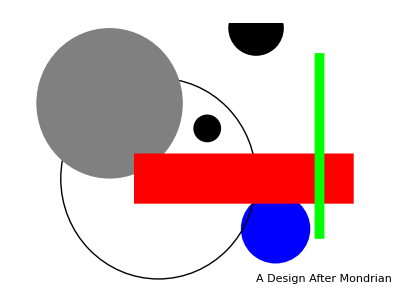

```mathematica
Show[Mondrian]
```

In response to the command InputForm[figure] Mathematica responds by reporting how it went about assembling primitives to produce the figure in question, as the following examples illustrate:

#### First Example

```mathematica
InputForm[Mondrian]
```

Graphics[{{PointSize[0.05], Point[{0.5, 0.5}]}, 
  {PointSize[0.1], Point[{1, 1.5}]}, 
  {RGBColor[0, 0, 1], PointSize[0.15], 
   Point[{1.2, -0.5}]}, Circle[{0, 0}, 1], 
  {GrayLevel[0.5], Disk[{-0.5, 0.75}, 0.75]}, 
  {RGBColor[1, 0, 0], Rectangle[{-0.25, -0.25}, 
    {2, 0.25}]}, {{RGBColor[0, 1, 0], 
    Rectangle[{1.6, -0.6}, {1.7, 1.25}]}, 
   Text["A Design After Mondrian", {1.7, -1}]}}]

#### Second Example

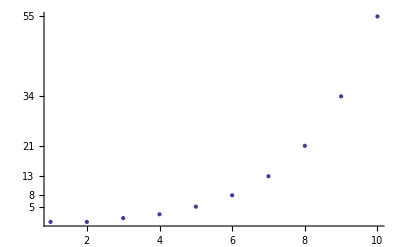

```mathematica
fib=Table[Fibonacci[n],{n,10}];
fibfigure=ListPlot[fib,PlotStyle->PointSize[Large], Ticks->{{2,4,6,8,10},{5,8,13,21,34,55}}, AxesOrigin->{0,0}]
```

```mathematica
InputForm[fibfigure]
```

Graphics[{Hue[0.67, 0.6, 0.6], PointSize[Large], 
  Point[{{1., 1.}, {2., 1.}, {3., 2.}, {4., 3.}, 
    {5., 5.}, {6., 8.}, {7., 13.}, {8., 21.}, 
    {9., 34.}, {10., 55.}}]}, 
 {AspectRatio -> GoldenRatio^(-1), Axes -> True, 
  AxesOrigin -> {0, 0}, PlotRange -> Automatic, 
  PlotRangeClipping -> True, 
  Ticks -> {{2, 4, 6, 8, 10}, {5, 8, 13, 21, 34, 
     55}}}]

#### Third Example

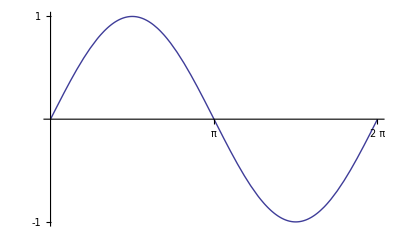

```mathematica
sinefigure=Plot[Sin[x],{x,0,2π}, Ticks->{{π,2π},{-1,+1}}]
```

```mathematica
InputForm[sinefigure]
```

Graphics[{{{}, {}, {Hue[0.67, 0.6, 0.6], 
    Line[{{1.2822827157509358*^-7, 
     1.2822827157509324*^-7}, 
     {0.0019271655319089223, 
     0.001927164339004283}, 
     {0.0038542028355462695, 
     0.00385419329326691}, 
     {0.007708277442820964, 
     0.007708201108565738}, 
     {0.015416426657370353, 
     0.015415816004008815}, 
     {0.030832725086469132, 
     0.03082784009467795}, {0.06166532194466669, 
     0.061626247826437476}, {0.1233305156610618, 
     0.12301810194283724}, {0.2570347881802097, 
     0.2542138749185557}, {0.3818787050494512, 
     0.3726645007390021}, {0.504273679847541, 
     0.4831716559080398}, {0.6370425397319885, 
     0.5948206667810294}, {0.7609510439665297, 
     0.6896104843619676}, {0.8952334332874284, 
     0.7803550768254575}, {0.8972933309007058, 
     0.7816415498416075}, {0.8993532285139831, 
     0.7829247062145637}, {0.9034730237405377, 
     0.7854810472663537}, {0.9117126141936469, 
     0.7905536910323366}, {0.9281917950998653, 
     0.8005376246467047}, {0.961150156912302, 
     0.8198506642936907}, {1.0270668805371757, 
     0.855785278429456}, {1.0289883350934232, 
     0.8567777264106476}, {1.0309097896496706, 
     0.8577670111800607}, {1.0347526987621656, 
     0.8597360764855387}, {1.0424385169871557, 
     0.8636360886325238}, {1.0578101534371358, 
     0.8712828366943681}, {1.088553426337096, 
     0.8859569678649591}, {1.0904748808933435, 
     0.886846439932971}, {1.092396335449591, 
     0.8877326377759202}, {1.0962392445620859, 
     0.8894951977114104}, {1.103925062787076, 
     0.8929808837325072}, {1.119296699237056, 
     0.8997938037956826}, {1.1500399721370163, 
     0.9127802676472789}, {1.152123518647738, 
     0.913629312329887}, {1.15420706515846, 
     0.9144743907973655}, {1.1583741581799036, 
     0.9161526344296697}, {1.166708344222791, 
     0.9194613668487993}, {1.1833767163085658, 
     0.9258870137580502}, {1.2167134604801153, 
     0.9379648812640387}, {1.2187970069908372, 
     0.9386852734597928}, {1.220880553501559, 
     0.9394015906683686}, {1.2250476465230027, 
     0.9408219877030862}, {1.23338183256589, 
     0.9436137462886434}, {1.2500502046516648, 
     0.9490004488089846}, {1.2833869488232146, 
     0.9589814532774429}, {1.2853320522769067, 
     0.9595310149939811}, {1.2872771557305986, 
     0.9600769463956869}, {1.291167362637983, 
     0.9611579100063794}, {1.298947776452751, 
     0.9632761834893663}, {1.3145086040822878, 
     0.9673376713325591}, {1.3164537075359797, 
     0.9678289078627277}, {1.3183988109896718, 
     0.9683164826835982}, {1.3222890178970559, 
     0.9692806398324919}, {1.3300694317118242, 
     0.9711649333808123}, {1.3456302593413607, 
     0.9747570429220562}, {1.3475753627950526, 
     0.9751894785134673}, {1.3495204662487448, 
     0.9756182245474039}, {1.3534106731561288, 
     0.9764646414683034}, {1.3611910869708972, 
     0.9781131301827487}, {1.3767519146004337, 
     0.9812323825384774}, {1.3786970180541256, 
     0.9816055983862323}, {1.3806421215078177, 
     0.9819751004015963}, {1.3845323284152018, 
     0.982702957357274}, {1.3923127422299701, 
     0.9841140447107248}, {1.4078735698595066, 
     0.9867574189497462}, {1.409780408593337, 
     0.9870649196839719}, {1.4116872473271673, 
     0.9873688314177196}, {1.415500924794828, 
     0.9879658834767021}, {1.4231282797301492, 
     0.9891168718422977}, {1.4250351184639793, 
     0.989395630363058}, {1.4269419571978097, 
     0.9896707914087998}, {1.4307556346654704, 
     0.9902103170863328}, {1.4383829896007918, 
     0.9912461555962515}, {1.4402898283346222, 
     0.9914961070359759}, {1.4421966670684525, 
     0.9917424533632795}, {1.446010344536113, 
     0.992224327110842}, {1.4536376994714342, 
     0.9931447747237425}, {1.4688924093420768, 
     0.9948122874129468}, {1.470799248075907, 
     0.9950044569152444}, {1.4727060868097372, 
     0.9951930085486457}, {1.476519764277398, 
     0.9955592554795967}, {1.4841471192127194, 
     0.9962483056308926}, {1.4860539579465497, 
     0.9964115137227522}, {1.48796079668038, 
     0.9965710988296106}, {1.4917744741480405, 
     0.9968793977804729}, {1.4994018290833617, 
     0.9974524952137558}, {1.501308667817192, 
     0.9975867039163834}, {1.5032155065510224, 
     0.9977172853609797}, {1.5070291840186831, 
     0.9979675645900754}, {1.5089360227525135, 
     0.9980872614645513}, {1.5108428614863438, 
     0.9982033292609522}, {1.5146565389540043, 
     0.998424575944621}, {1.5165633776878344, 
     0.9985297540274285}, {1.5184702164216648, 
     0.9986313014232436}, {1.5222838938893255, 
     0.9988235026901806}, {1.5241907326231559, 
     0.9989141558624522}, {1.5260975713569862, 
     0.9990011769500338}, {1.529911248824647, 
     0.9991643216186877}, {1.5319801795129515, 
     0.9992467479388707}, {1.5340491102012561, 
     0.9993248970106624}, {1.5361180408895607, 
     0.9993987684995479}, {1.5381869715778655, 
     0.9994683620893222}, {1.5402559022661704, 
     0.999533677482092}, {1.542324832954475, 
     0.9995947143982763}, {1.5464626943310842, 
     0.9997039517741367}, {1.5485316250193888, 
     0.9997521517662251}, {1.5506005557076934, 
     0.9997960723465549}, {1.552669486395998, 
     0.9998357133271253}, {1.5547384170843028, 
     0.9998710745382542}, {1.5568073477726077, 
     0.9999021558285789}, {1.5588762784609123, 
     0.9999289570650568}, {1.5609452091492169, 
     0.9999514781329658}, {1.5630141398375215, 
     0.9999697189359052}, {1.565083070525826, 
     0.9999836793957958}, {1.5671520012141307, 
     0.9999933594528801}, {1.5692209319024353, 
     0.9999987590657231}, {1.57128986259074, 
     0.9999998782112116}, {1.573358793279045, 
     0.9999967168845553}, {1.5754277239673495, 
     0.9999892750992861}, {1.5774966546556541, 
     0.9999775528872585}, {1.5795655853439587, 
     0.999961550298649}, {1.5816345160322633, 
     0.9999412674019562}, {1.583703446720568, 
     0.9999167042840006}, {1.5857723774088726, 
     0.9998878610499239}, {1.5878413080971774, 
     0.9998547378231887}, {1.5899102387854822, 
     0.9998173347455782}, {1.5919791694737868, 
     0.9997756519771952}, {1.5940481001620914, 
     0.9997296896964616}, {1.596117030850396, 
     0.9996794481001177}, {1.5981859615387006, 
     0.9996249274032214}, {1.6002548922270052, 
     0.9995661278391469}, {1.6023238229153098, 
     0.9995030496595841}, {1.6043927536036147, 
     0.9994356931345377}, {1.6064616842919195, 
     0.9993640585523252}, {1.608530614980224, 
     0.9992881462195765}, {1.6126684763568333, 
     0.9991234896205428}, {1.614737407045138, 
     0.9990347460590658}, {1.6168063377334425, 
     0.9989417261566658}, {1.620944199110052, 
     0.9987428589400763}, {1.6292199218632706, 
     0.9982938271614664}, {1.6312888525515752, 
     0.9981708850461833}, {1.6333577832398798, 
     0.9980436702877108}, {1.6374956446164892, 
     0.9977764250376405}, {1.6457713673697079, 
     0.9971906880040196}, {1.6478402980580125, 
     0.9970335810141968}, {1.649909228746317, 
     0.9968722062493834}, {1.6540470901229263, 
     0.9965366561760906}, {1.662322812876145, 
     0.9958143743466595}, {1.6642533005074198, 
     0.9956360747050302}, {1.6661837881386945, 
     0.995454064545459}, {1.6700447634012443, 
     0.9950789153995656}, {1.677766713926344, 
     0.9942841216643886}, {1.6796972015576188, 
     0.9940761576460222}, {1.6816276891888937, 
     0.9938644889231839}, {1.6854886644514433, 
     0.9934300405332672}, {1.6932106149765427, 
     0.9925167229335421}, {1.6951411026078176, 
     0.9922791441397993}, {1.6970715902390925, 
     0.992037867338661}, {1.7009325655016423, 
     0.9915442233247193}, {1.7086545160267417, 
     0.990512599695223}, {1.7240984170769407, 
     0.9882722299515398}, {1.7260289047082156, 
     0.9879755986512128}, {1.7279593923394905, 
     0.987675285381863}, {1.7318203676020403, 
     0.9870636174266212}, {1.7395423181271397, 
     0.9857961480515994}, {1.7549862191773387, 
     0.9830849445640588}, {1.7858740212777366, 
     0.9769598153400458}, {1.7879666008634858, 
     0.9765110713568594}, {1.790059180449235, 
     0.9760580513413295}, {1.7942443396207335, 
     0.9751391911668498}, {1.8026146579637303, 
     0.9732502469670653}, {1.819355294649724, 
     0.9692679326365597}, {1.8528365680217114, 
     0.9604896062780456}, {1.8549291476074605, 
     0.9599051056843635}, {1.8570217271932097, 
     0.959316401773997}, {1.8612068863647082, 
     0.9581263943330792}, {1.869577204707705, 
     0.9556960543090358}, {1.8863178413936987, 
     0.9506346758110856}, {1.9197991147656859, 
     0.9397141875380657}, {1.9218534296315735, 
     0.9390097098112606}, {1.9239077444974608, 
     0.9383012692680873}, {1.9280163742292356, 
     0.936872511708413}, {1.9362336336927854, 
     0.9339675754613147}, {1.9526681526198852, 
     0.9279687105727975}, {1.9855371904740848, 
     0.9152207709228335}, {2.0512752661824836, 
     0.8867736568214568}, {2.053191137991341, 
     0.8858865063862249}, {2.055107009800199, 
     0.8849961042481709}, {2.058938753417914, 
     0.883205557948632}, {2.066602240653345, 
     0.8795855895181172}, {2.081929215124206, 
     0.8721908974026384}, {2.112583164065929, 
     0.8567886352600307}, {2.1738910619493748, 
     0.8235842465112402}, {2.175969025712707, 
     0.8224038607722788}, {2.178046989476039, 
     0.8212199239494951}, {2.182202917002703, 
     0.818841417516406}, {2.190514772056031, 
     0.8140420176039472}, {2.207138482162687, 
     0.804274835207209}, {2.2403859023759995, 
     0.7840764676698918}, {2.306880742802624, 
     0.7411031219178127}, {2.4310100680059663, 
     0.6522754710746894}, {2.5655132782956667, 
     0.5447402771484026}, {2.697567546514215, 
     0.4295777271320345}, {2.820761459082857, 
     0.3153554511260218}, {2.954329256737857, 
     0.1861708352681441}, {3.0790366987429505, 
     0.06251516334017572}, {3.2012951986768923, 
     -0.05966708417636863}, {3.3339275836971916, 
     -0.19115128932767658}, {3.4576996130675846, 
     -0.3108687742575189}, {3.5918455275243355, 
     -0.43519321980343784}, {3.7235424999099345, 
     -0.549653867612323}, {3.846379116645627, 
     -0.6478711825589065}, {3.9795896184676773, 
     -0.7433046755726646}, {3.981532589501617, 
     -0.7446030280816351}, {3.983475560535557, 
     -0.7458985696134667}, {3.987361502603436, 
     -0.7484812001929632}, {3.9951333867391954, 
     -0.7536125151423854}, {4.010677155010713, 
     -0.7637382790138112}, {4.041764691553749, 
     -0.7834338385481847}, {4.103939764639821, 
     -0.8205354257281964}, {4.105844470953899, 
     -0.8216226585479436}, {4.107749177267976, 
     -0.8227069105987015}, {4.111558589896132, 
     -0.8248664566698257}, {4.1191774151524445, 
     -0.8291496072337002}, {4.134415065665069, 
     -0.8375712755391325}, {4.164890366690317, 
     -0.8538292962794404}, {4.166795073004395, 
     -0.8548192476558022}, {4.168699779318473, 
     -0.855806097829102}, {4.172509191946629, 
     -0.8577704802569843}, {4.180128017202941, 
     -0.861661873902663}, {4.195365667715565, 
     -0.8692943895789487}, {4.225840968740814, 
     -0.8839521934370734}, {4.227907767009366, 
     -0.884916692708362}, {4.229974565277918, 
     -0.8858774119221076}, {4.234108161815023, 
     -0.8877874937776966}, {4.242375354889233, 
     -0.8915621173125434}, {4.258909741037652, 
     -0.8989283062064903}, {4.291978513334489, 
     -0.9129214911665804}, {4.294045311603041, 
     -0.9137630738725799}, {4.2961121098715935, 
     -0.9146007532992904}, {4.300245706408699, 
     -0.9162643880184258}, {4.308512899482908, 
     -0.9195446617800588}, {4.325047285631326, 
     -0.9259164475524849}, {4.358116057928164, 
     -0.9378989661064421}, {4.360044413139687, 
     -0.9385661847535481}, {4.36197276835121, 
     -0.9392299132928623}, {4.365829478774255, 
     -0.9405468901886643}, {4.373542899620345, 
     -0.9431388549606081}, {4.3889697413125255, 
     -0.948154293060208}, {4.419823424696887, 
     -0.9575070963446649}, {4.421751779908409, 
     -0.9580614720957839}, {4.423680135119932, 
     -0.9586122852448582}, {4.427536845542977, 
     -0.9597032155572174}, {4.435250266389067, 
     -0.9618422357239117}, {4.450677108081248, 
     -0.9659484732670754}, {4.481530791465609, 
     -0.9734703886979993}, {4.483621238631606, 
     -0.9739465828809345}, {4.485711685797603, 
     -0.9744185209487001}, {4.489892580129597, 
     -0.9753496205079142}, {4.498254368793584, 
     -0.9771606567479661}, {4.51497794612156, 
     -0.9805776407913966}, {4.517068393287556, 
     -0.9809855000855563}, {4.519158840453553, 
     -0.9813890725047052}, {4.523339734785547, 
     -0.982183349682318}, {4.531701523449534, 
     -0.9837203851951678}, {4.54842510077751, 
     -0.9865880110231746}, {4.550515547943506, 
     -0.9869270791939445}, {4.552605995109504, 
     -0.9872618345251946}, {4.556786889441497, 
     -0.987918400836508}, {4.565148678105485, 
     -0.9891797162821415}, {4.567239125271482, 
     -0.989484241832617}, {4.5693295724374785, 
     -0.9897844433688542}, {4.573510466769473, 
     -0.9903718691700315}, {4.58187225543346, 
     -0.9914947761459183}, {4.583962702599457, 
     -0.9917646739089758}, {4.586053149765454, 
     -0.9920302376923803}, {4.590234044097448, 
     -0.9925483586971543}, {4.598595832761435, 
     -0.9935325431581933}, {4.615319410089411, 
     -0.9952924474135678}, {4.6172714141983775, 
     -0.9954797338799681}, {4.619223418307345, 
     -0.995663227251192}, {4.623127426525279, 
     -0.9960188319258931}, {4.630935442961148, 
     -0.9966844943384429}, {4.6328874470701145, 
     -0.9968414172764121}, {4.634839451179082, 
     -0.9969945419307571}, {4.638743459397016, 
     -0.9972893940692339}, {4.646551475832885, 
     -0.9978334942406683}, {4.648503479941851, 
     -0.9979600153836806}, {4.650455484050819, 
     -0.9980827339808533}, {4.654359492268753, 
     -0.9983167616817821}, {4.65631149637772, 
     -0.998428069893818}, {4.6582635004866875, 
     -0.9985355737765774}, {4.662167508704622, 
     -0.9987391669302672}, {4.664119512813588, 
     -0.9988352554254427}, {4.666071516922556, 
     -0.9989275380398349}, {4.66997552514049, 
     -0.9991006842342673}, {4.671927529249457, 
     -0.9991815471545655}, {4.673879533358424, 
     -0.9992586028745983}, {4.677783541576359, 
     -0.9994012915539486}, {4.679735545685325, 
     -0.9994669239695767}, {4.681687549794293, 
     -0.9995287480975628}, {4.6836395539032605, 
     -0.9995867637023375}, {4.685591558012227, 
     -0.9996409705628425}, {4.687543562121194, 
     -0.9996913684725326}, {4.689495566230161, 
     -0.9997379572393758}, {4.691447570339129, 
     -0.9997807366858539}, {4.693399574448096, 
     -0.9998197066489635}, {4.695351578557062, 
     -0.9998548669802167}, {4.69730358266603, 
     -0.9998862175456416}, {4.699255586774997, 
     -0.9999137582257822}, {4.701207590883964, 
     -0.9999374889157}, {4.703159594992931, 
     -0.9999574095249734}, {4.705111599101898, 
     -0.9999735199776986}, {4.707063603210866, 
     -0.9999858202124895}, {4.709015607319833, 
     -0.9999943101824783}, {4.710967611428799, 
     -0.9999989898553157}, {4.712919615537767, 
     -0.9999998592131705}, {4.714871619646734, 
     -0.9999969182527302}, {4.716823623755701, 
     -0.9999901669852007}, {4.718775627864668, 
     -0.9999796054363067}, {4.720727631973635, 
     -0.9999652336462909}, {4.722679636082603, 
     -0.9999470516699144}, {4.72463164019157, 
     -0.9999250595764564}, {4.726583644300536, 
     -0.9998992574497138}, {4.728535648409504, 
     -0.9998696453880008}, {4.730487652518471, 
     -0.9998362235041489}, {4.732439656627438, 
     -0.9997989919255063}, {4.734391660736405, 
     -0.9997579507939368}, {4.736343664845372, 
     -0.9997131002658205}, {4.7402476730633065, 
     -0.9996119717180407}, {4.742161412452412, 
     -0.9995568338809567}, {4.744075151841518, 
     -0.9994980352695916}, {4.747902630619728, 
     -0.9993694565987994}, {4.749816370008833, 
     -0.9992996770102786}, {4.751730109397938, 
     -0.9992262375892872}, {4.755557588176149, 
     -0.9990683803391527}, {4.757471327565255, 
     -0.9989839630881456}, {4.75938506695436, 
     -0.9988958871609377}, {4.763212545732571, 
     -0.9987087605815942}, {4.770867503288993, 
     -0.9982906183991543}, {4.772781242678098, 
     -0.9981769415206926}, {4.774694982067203, 
     -0.9980596089216637}, {4.778522460845414, 
     -0.9978139782941661}, {4.786177418401836, 
     -0.9972788681968285}, {4.788091157790942, 
     -0.9971359583355132}, {4.790004897180047, 
     -0.9969893965661247}, {4.7938323759582575, 
     -0.9966853194635711}, {4.801487333514679, 
     -0.9960333668752152}, {4.803401072903784, 
     -0.9958612575275346}, {4.80531481229289, 
     -0.9956855009402419}, {4.8091422910711, 
     -0.9953230486349366}, {4.8167972486275215, 
     -0.9945544063660269}, {4.818710988016627, 
     -0.9943531378725057}, {4.820624727405733, 
     -0.9941482276627056}, {4.824452206183943, 
     -0.9937274851094541}, {4.832107163740364, 
     -0.9928423333212237}, {4.83402090312947, 
     -0.9926119528569672}, {4.835934642518575, 
     -0.9923779370533432}, {4.839762121296785, 
     -0.991899002869539}, {4.847417078853207, 
     -0.9908975490317617}, {4.86272699396605, 
     -0.988720509333535}, {4.86480282530963, 
     -0.988407477199899}, {4.86687865665321, 
     -0.9880901859450845}, {4.871030319340369, 
     -0.9874428315591933}, {4.879333644714688, 
     -0.9860970747203687}, {4.895940295463326, 
     -0.9832016996684034}, {4.8980161268069065, 
     -0.9828206959267954}, {4.900091958150486, 
     -0.9824354571378642}, {4.904243620837645, 
     -0.9816522810763635}, {4.912546946211964, 
     -0.9800351826482793}, {4.929153596960601, 
     -0.9765983969046794}, {4.9312294283041815, 
     -0.9761498418106058}, {4.933305259647761, 
     -0.9756970804144146}, {4.9374569223349205, 
     -0.9747789465377251}, {4.945760247709239, 
     -0.9728922902155126}, {4.962366898457876, 
     -0.9689178846305395}, {4.9955801999551515, 
     -0.9601686346199421}, {4.997517588241701, 
     -0.9596254856638143}, {4.999454976528251, 
     -0.9590787347801046}, {5.003329753101351, 
     -0.9579744354523093}, {5.0110793062475505, 
     -0.9557227048680353}, {5.02657841253995, 
     -0.9510471938096906}, {5.057576625124749, 
     -0.9410119752114029}, {5.059514013411299, 
     -0.9403546492016023}, {5.061451401697849, 
     -0.9396937935967685}, {5.065326178270949, 
     -0.9383615035372543}, {5.073075731417148, 
     -0.9356546783064531}, {5.088574837709547, 
     -0.9300726207859755}, {5.119573050294346, 
     -0.9182396411990768}, {5.1216725305353705, 
     -0.9174061710059188}, {5.1237720107763955, 
     -0.9165686570554701}, {5.127970971258444, 
     -0.9148815126669392}, {5.13636889222254, 
     -0.9114588624253163}, {5.153164734150735, 
     -0.9044209668719675}, {5.186756418007123, 
     -0.8895818387807382}, {5.253939785719899, 
     -0.8569103254512629}, {5.256001001241062, 
     -0.8558460203515067}, {5.258062216762224, 
     -0.8547780790975703}, {5.262184647804549, 
     -0.8526313062916386}, {5.270429509889199, 
     -0.8482943275018867}, {5.286919234058499, 
     -0.8394476742174763}, {5.319898682397099, 
     -0.8210720854972529}, {5.3858575790743, 
     -0.781663003875219}, {5.508915016778795, 
     -0.6991945692154065}, {5.642346339569648, 
     -0.5978681634714186}, {5.766917306710594, 
     -0.49363798436551354}, {5.889039331780388, 
     -0.38401978680018356}, {6.02153524193654, 
     -0.2586748077041959}, {6.145170796442786, 
     -0.13757677765618304}, {6.279180236035389, 
     -0.004005060436919016}, {6.27924281326845, 
     -0.003942483697944346}, {6.279305390501511, 
     -0.003879906943531263}, {6.279430544967634, 
     -0.003754753389369155}, {6.27968085389988, 
     -0.0035044461065668678}, 
     {6.2801814717643705, 
     -0.0030038308979366004}, 
     {6.281182707493352, 
     -0.0020025983476951096}, 
     {6.281245284726413, 
     -0.0019400212362338171}, 
     {6.281307861959474, 
     -0.0018774441171755757}, 
     {6.281433016425598, 
     -0.0017522898572475442}, 
     {6.281683325357843, 
     -0.0015019812570110267}, 
     {6.282183943222334, 
     -0.0010013637899030433}, 
     {6.282246520455395, 
     -0.0009387865862961498}, 
     {6.282309097688456, 
     -0.0008762093790130525}, 
     {6.282434252154579, -0.000751054954397545}, 
     {6.282684561086825, 
     -0.0005007460718350281}, 
     {6.282747138319886, 
     -0.00043816884567981243}, 
     {6.282809715552947, -0.000375591617808767}, 
     {6.282934870019069, 
     -0.0002504371578993739}, {6.28299744725213, 
     -0.0001878599263511199}, 
     {6.2830600244851915, 
     -0.0001252826940672233}, 
     {6.283122601718253, 
     -0.00006270546129273089}, 
     {6.283185178951315, 
     -1.28228271801381*^-7}}]}}}, 
 {AspectRatio -> GoldenRatio^(-1), Axes -> True, 
  AxesOrigin -> {0, 0}, PlotRange -> 
   {{0, 2*Pi}, {-0.9999998592131705, 
     0.9999998782112116}}, PlotRangeClipping -> 
   True, PlotRangePadding -> {Scaled[0.02], 
    Scaled[0.02]}, Ticks -> {{Pi, 2*Pi}, 
    {-1, 1}}}]

This fulsome output provides vivid evidence of why people have tended to avoid accurate figures by hand! And why they can never hope to achieve the accurate detail that Mathematica insists upon achieving.

To learn more about this subject, go to Help > Documentation Center and, in the search window, ask first about ref/Graphics and then about tutorial/TheStructureOfGraphics.

### The Graphics Menu

New to v.6 are the resouces made available by the Graphics menu.

Consult Help > Documentation Center and, in the search window, ask about guide/GraphicsMenu.

Go first to Graphics > New Graphic (which introduces a rectangular space upon which to draw), then to Graphics > Drawing Tools, which produces a tablet displaying various tools you can  use to construct a graphic very much as you would draw on a piece of paper: Mathematica automatically converts you art into a sequence of primitive graphic commands.

#### Example

I sketched the following figure

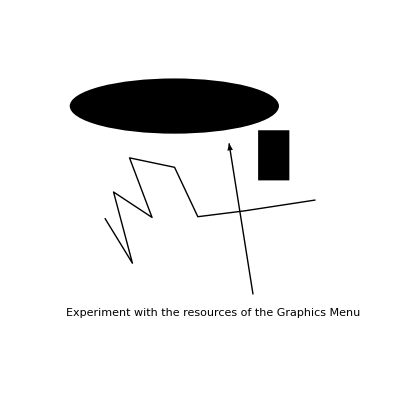

and then Copy/Pasted it into the following definition:

```mathematica
Doodle=-Graphics-;
```

```mathematica
Show[Doodle]
```

-Graphics-

This, according to Mathematica, is what I did:

```mathematica
InputForm[Doodle]
```

Graphics[{Disk[{0.42000000000000004, 
    0.788888888888889}, {0.31999999999999995, 
    0.08444444444444454}], 
  Rectangle[{0.6777777777777778, 
    0.7133333333333335}, {0.7733333333333333, 
    0.5600000000000002}], 
  Line[{{0.20888888888888887, 
     0.44444444444444453}, {0.29333333333333333, 
     0.30666666666666675}, {0.23555555555555555, 
     0.5244444444444445}, {0.3533333333333333, 
     0.44666666666666677}, {0.2844444444444444, 
     0.6288888888888889}, {0.4222222222222223, 
     0.6000000000000001}, {0.4933333333333333, 
     0.4488888888888889}, {0.6355555555555555, 
     0.4666666666666667}, {0.8533333333333333, 
     0.5}}], Arrow[{{0.6622222222222222, 
     0.21111111111111125}, {0.5888888888888888, 
     0.6733333333333336}}], Inset[Null, 
   {0.37111111111111106, 0.19777777777777783}, 
   {-1., 0.}], Style[Inset[Cell["Experiment with \
the resources of the Graphics Menu"], 
    {0.09111111111111109, 0.1555555555555558}, 
    {-1., 0.}], StripOnInput -> False, 
   FontSize -> 14]}, PlotRange -> 
  {{0, 1}, {0, 1}}]

SUGGESTION: Try similar experiments.

The command

```mathematica
?Arrow
```

Arrow[{{x_1,y_1},{x_2,y_2}}] is a graphics primitive which represents an arrow from (x_1,y_1) to (x_2,y_2). 
Arrow[{pt_1,pt_2},s] represents an arrow with its ends set back from pt_1 and pt_2 by a distance s. 
Arrow[{pt_1,pt_2},{s_1,s_2}] sets back by s_1 from pt_1 and s_2 from pt_2.

(follow the ≫) provides a specialized variant of the resources made avilable by the Graphics Menu.

#### Example

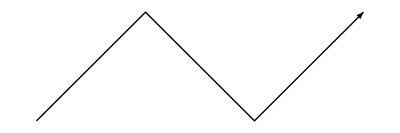

```mathematica
Graphics[{Arrowheads[Large],Arrow[{{1,0},{2,1},{3,0},{4,1}}]}]
```

### Graphical Representation of Vector Fields

As physicists, we spend a lot of time thinking about "vector fields" of various sorts (they might be electric/magnetic/gravitational force fields, or might refer to some kind of "flow," etc.)…but we seldom attempt to draw pictures of such objects.  Mathematica takes the pain out of that exercise, and the results are often quite informative.

To gain access to that powerful resource one must import the Vector Field Plotting Package …but, before we do so, I interpolate a general comment concerning

#### The Preferred Way to Load Packages

Two alternative commands are available, the Needs command

```mathematica
?Needs
```

Needs[context`] loads an appropriate file if the specified context is not already in $Packages. 
Needs[context`,file] loads file if the specified context is not already in $Packages.

and the Get command (of which << is the symbolic name):

```mathematica
?Get
```

<<name reads in a file, evaluating each expression in it, and returning the last one.

```mathematica
?<<
```

<<name reads in a file, evaluating each expression in it, and returning the last one.

Mathematica tends to become caught up in an endless loop and crash when asked to "get" something that has already been "got," whereas Needs undertakes to get the thing only if it has not already been got, and thus avoids such difficulties. Needs—not <<—is therefore the preferred (because least hazardous) command.

Returning now to the main line of the present discussion, we import the package

```mathematica
Needs["VectorFieldPlots`"]
```

and inquire about its contents:

```mathematica
?VectorFieldPlot
```

VectorFieldPlot[{f_x,f_y},{x,x_min,x_max},{y,y_min,y_max}] generates a plot of the vector field given by the vector valued function {f_x,f_y} as a function of x and y.
VectorFieldPlot[{f_x,f_y},{x,x_min,x_max,dx},{y,y_min,y_max,dy}] uses steps dx in variable x, and steps dy in variable y.

Click on the ≫, then on the MORE ABOUT at the bottom of the page and discover that the package supplies several additional commands—most notably

```mathematica
?GradientFieldPlot
?HamiltonianFieldPlot
```

GradientFieldPlot[f,{x,x_min,x_max},{y,y_min,y_max}] generates a plot of the gradient vector field of the scalar function f.
GradientFieldPlot[f,{x,x_min,x_max,dx},{y,y_min,y_max,dy}] uses steps dx in variable x, and steps dy in variable y.

HamiltonianFieldPlot[f,{x,x_min,x_max},{y,y_min,y_max}] generates a plot of the Hamiltonian vector field of the scalar-valued function f as a function of x and y.
HamiltonianFieldPlot[f,{x,x_min,x_max,dx},{y,y_min,y_max,dy}] uses steps dx in variable x, and steps dy in variable y.

and their 3D analogs, which are of especial interest to physicists.

#### Example

A 2-dimensional vector field is a 2-element list, of the form {V_x[x,y], V_y[x,y]}. Consider this specific example:

```mathematica
vectorfield[x_,y_]:={x^4+y^4-6 x^2 y^2-1,4x y^3-4 x^3 y}
```

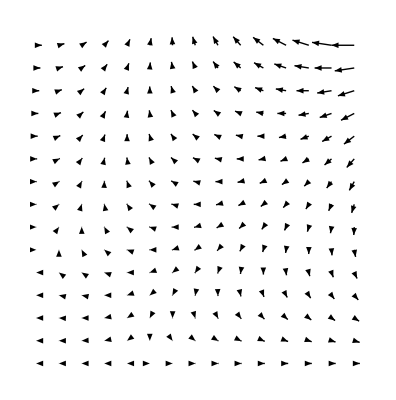

```mathematica
VectorFieldPlot[vectorfield[x,y],{x,0,3},{y,0,3}]
```

#### A More Interesting Example: Electric Dipole

The potential in the vicinity of an electric dipole can be described

```mathematica
dipolepotential[x_,y_]:=1/(√(.1+x^2+(y-1)^2))-1/(√(.1+x^2+(y+1)^2))
```

REMARK: The blue terms on the right have been introduced (by me,  by hand) to temper the singularities which occur at the positions of the ± charges.

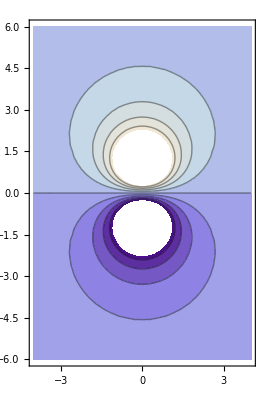

```mathematica
equipotentials=ContourPlot[dipolepotential[x,y],{x,-4,4},{y,-6,6}, AspectRatio->Automatic]
```

REMARK: The AspectRatio → Automatic has been introduced to keep the figure from becoming deceptively squashed in the y-direction. Execute the command with that detail omitted and see what you get.

The electric field (a vector field) is the negative gradient of the potential, and has the form shown below:

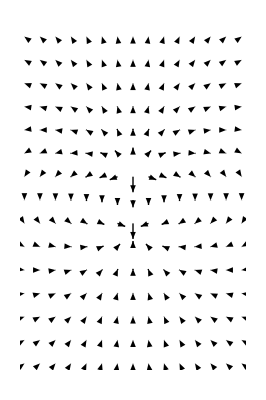

```mathematica
dipolefield=GradientFieldPlot[-dipolepotential[x,y],{x,-4,4},{y,-6,6}, 
AspectRatio->Automatic]
```

It is instructive to superimpose the two preceding figures:

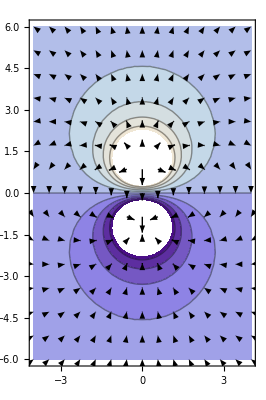

```mathematica
Show[equipotentials, dipolefield]
```

#### Example: 3-Dimensional Gradient Field

```mathematica
Scalarfield[x_,y_,z_]:=x^2 y-z
```

```mathematica
AssciatedVectorField=GradientFieldPlot3D[Scalarfield[x,y,z],{x,0,1},{y,0,1},{z,0,1}]
```

-Graphics3D-

```mathematica
AssciatedVectorField=GradientFieldPlot3D[Scalarfield[x,y,z],{x,0,1},{y,0,1},{z,0,1}, VectorHeads->True]
```

-Graphics3D-

Use the mouse to view this figure from various angles.

Look now to what in some contexts would be called "equipotential surfaces":

```mathematica
SurfacesOfConstantValue=ContourPlot3D[Scalarfield[x,y,z],{x,0,1},{y,0,1},{z,0,1},ContourStyle->Directive[Orange,Opacity[0.8],Specularity[White,30]] ]
```

-Graphics3D-

Here we superimpose the preceding figures:

```mathematica
Show[AssciatedVectorField,SurfacesOfConstantValue]
```

-Graphics3D-

It is evident—most vividly evident if you view the composite figure from the appropriate angle—that the magnitudes of the gradient vectors are indicated not by the length of the arrows (all have the same length) but by the relative sizes of their arrowheads.

### Polyhedra

Mathematica 5.2 was supplemented by standard packages—called Graphics`Shapes` and Graphics`Polyhedra`—that provided images and other information about a variety of 3D geometrical forms.  In Mathematica 6 the information formerly available Graphics`Shapes` in has been dispersed to a variety of other sources: in the Documentation Center search for Compatibility/tutorial/Graphics/Shapes to learn about those, which include Torus, MobiusStrip, DoubleHelix and such like.  But the information formerly provided in Graphics`Polyhedra` has in v.6 been written directly into the Kernel. Here I can only hint at the richness of that resource, which I have on occasion found to be quite useful: for further information, return to the Documentation Center and search for ref/PolyhedronData.

```mathematica
PolyhedronData["Dodecahedron"]
```

-Graphics3D-

View the figure from various angles.

The following commands provide various kinds of information about (in this instance) the dodecahedron:

```mathematica
PolyhedronData["Dodecahedron", "VertexCount"]
PolyhedronData["Dodecahedron", "EdgeCount"]
PolyhedronData["Dodecahedron", "FaceCount"]
```

20

30

12

```mathematica
PolyhedronData["Dodecahedron", "VertexCoordinates"]
```

{{0,0,√(9/8+(3 √5)/8)},{0,0,-1/2 √(3/2 (3+√5))},{√(1/8-(√5)/24),1/4 (-3-√5),√(1/8+(√5)/24)},{√(1/8-(√5)/24),1/4 (3+√5),√(1/8+(√5)/24)},{√(1/8+(√5)/24),1/4 (-1-√5),-1/2 √(5/6 (3+√5))},{√(1/8+(√5)/24),1/4 (1+√5),-1/2 √(5/6 (3+√5))},{√(5/8+(5 √5)/24),1/4 (-1-√5),√(1/8+(√5)/24)},{√(5/8+(5 √5)/24),1/4 (1+√5),√(1/8+(√5)/24)},{-√(3/4+(√5)/3),-1/2,√(1/8+(√5)/24)},{-√(3/4+(√5)/3),1/2,√(1/8+(√5)/24)},{√(3/4+(√5)/3),-1/2,-1/2 √(1/6 (3+√5))},{√(3/4+(√5)/3),1/2,-1/2 √(1/6 (3+√5))},{-√(1/6 (3+√5)),0,-1/2 √(5/6 (3+√5))},{-1/2 √(1/6 (3+√5)),1/4 (-1-√5),√(5/8+(5 √5)/24)},{-1/2 √(1/6 (3+√5)),1/4 (1+√5),√(5/8+(5 √5)/24)},{√(1/6 (3+√5)),0,√(5/8+(5 √5)/24)},{-1/2 √(5/6 (3+√5)),1/4 (-1-√5),-1/2 √(1/6 (3+√5))},{-1/2 √(5/6 (3+√5)),1/4 (1+√5),-1/2 √(1/6 (3+√5))},{Root[1-36 #1^2+144 #1^4&,2],1/4 (-3-√5),-1/2 √(1/6 (3+√5))},{Root[1-36 #1^2+144 #1^4&,2],1/4 (3+√5),-1/2 √(1/6 (3+√5))}}

The output here has been a list of 20 3-vectors. Here are the numerical values of their coordinates:

```mathematica
N[%]
```

{{0.,0.,1.40126},{0.,0.,-1.40126},{0.178411,-1.30902,0.467086},{0.178411,1.30902,0.467086},{0.467086,-0.809017,-1.04444},{0.467086,0.809017,-1.04444},{1.04444,-0.809017,0.467086},{1.04444,0.809017,0.467086},{-1.22285,-0.5,0.467086},{-1.22285,0.5,0.467086},{1.22285,-0.5,-0.467086},{1.22285,0.5,-0.467086},{-0.934172,0.,-1.04444},{-0.467086,-0.809017,1.04444},{-0.467086,0.809017,1.04444},{0.934172,0.,1.04444},{-1.04444,-0.809017,-0.467086},{-1.04444,0.809017,-0.467086},{-0.178411,-1.30902,-0.467086},{-0.178411,1.30902,-0.467086}}

Here I use

```mathematica
?ListPointPlot3D
```

ListPointPlot3D[{{x_1,y_1,z_1},{x_2,y_2,z_2},…}] generates a 3D scatter plot of points with coordinates {x_i,y_i,z_i}. 
ListPointPlot3D[array] generates a 3D scatter plot of points with a 2D array of height values.
ListPointPlot3D[{data_1,data_2,…}] plots several collections of points, by default in different colors.

(which I previously declined to discuss, on the ground that it was "seldom useful") to construct a graphic display of that data:

```mathematica
ListPointPlot3D[PolyhedronData["Dodecahedron", "VertexCoordinates"], AspectRatio->Automatic, PlotStyle->PointSize[0.03],BoxRatios->{1,1,1}, Ticks->False]
```

-Graphics3D-

View the figure from a variety of angles!

If any doubt remains concerning the richness of this resouce, consider the following tiny sampling of the possibilities:

```mathematica
PolyhedronData["Platonic"]
PolyhedronData["Archimedean"]
```

{Cube,Dodecahedron,Icosahedron,Octahedron,Tetrahedron}

{Cuboctahedron,GreatRhombicosidodecahedron,GreatRhombicuboctahedron,Icosidodecahedron,SmallRhombicosidodecahedron,SmallRhombicuboctahedron,SnubCube,SnubDodecahedron,TruncatedCube,TruncatedDodecahedron,TruncatedIcosahedron,TruncatedOctahedron,TruncatedTetrahedron}

```mathematica
PolyhedronData["Icosidodecahedron"]
```

-Graphics3D-

```mathematica
PolyhedronData["GreatRhombicuboctahedron"]
```

-Graphics3D-

```mathematica
PolyhedronData["GyroelongatedPentagonalBicupola"]
```

-Graphics3D-

```mathematica
PolyhedronData["SmallStellatedDodecahedron"]
```

-Graphics3D-

This final command takes a bit longer to run: you might collect paper and scissors while waiting.

```mathematica
GraphicsGrid[Partition[Graphics[Tooltip[PolyhedronData[#,"NetImage"][[1]],PolyhedronData[#,"Name"]]]&/@PolyhedronData["NetImage","Defined"],10]]
```

-Graphics-

For a large collection of design-it-yourself rotatable polyhedra, visit .

### Composite Figures

Frequently one has need to display related figures in a way that facilitates their comparison.  I review here some some techniques standard to printed publication, my main objective being to prepare the ground for discussion of a much more vividly powerful technique that was made possible by the invention of electronic modes of publication.

Some of the relevant commands employed in this connection by Mathematica 6 differ from those used in earlier versions of Mathematica. Most notably, GraphicsArray has been superseded by GraphicsGrid and Grid.  To read about the details, go to the Documentation Center and search for tutorial/RedrawingAndCombiningPlots.

We begin by introducing a population of functions that acquire importance for physicists because they describe the "eigenstates" of a quantum oscillator:

```mathematica
He[n_,x_]:=(1/√(2^n))HermiteH[n,x/√2]
Ψ[n_,x_]:=(1/√(n!√(2π)))ⅇ^(-1/4 x^2)He[n,x]
```

From such evidence as this

```mathematica
∫_(-∞)^∞ Ψ[0,x]Ψ[0,x]ⅆx
∫_(-∞)^∞ Ψ[1,x]Ψ[1,x]ⅆx
∫_(-∞)^∞ Ψ[0,x]Ψ[1,x]ⅆx
```

1

1

0

we infer that the Ψ-functions are orthonormal. A few Ψ-functions of low order are plotted below:

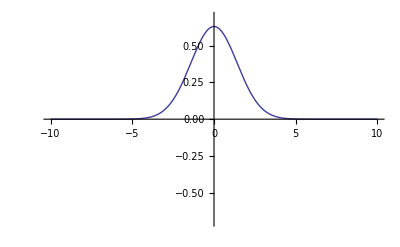

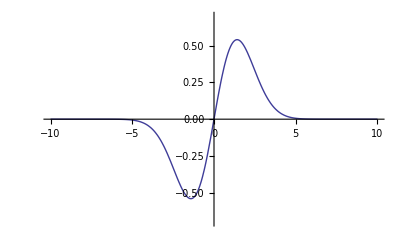

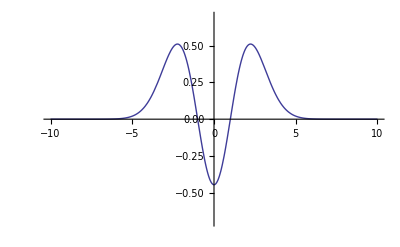

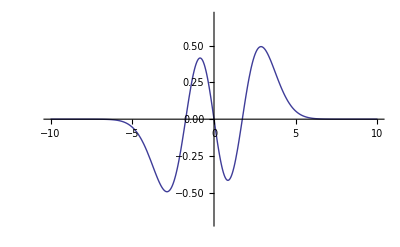

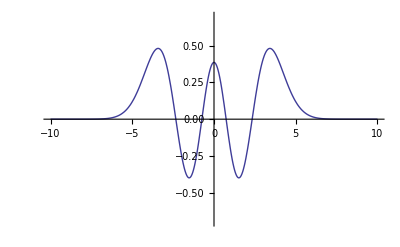

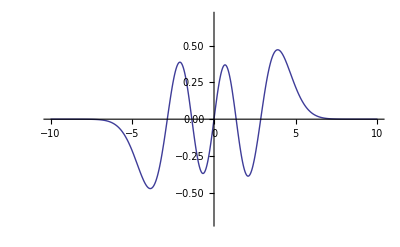

```mathematica
state1=Plot[Ψ[0,x],{x,-10,10}, PlotRange->{-0.7,0.7}]
state2=Plot[Ψ[1,x],{x,-10,10}, PlotRange->{-0.7,0.7}]
state3=Plot[Ψ[2,x],{x,-10,10}, PlotRange->{-0.7,0.7}]
state4=Plot[Ψ[3,x],{x,-10,10}, PlotRange->{-0.7,0.7}]
state5=Plot[Ψ[4,x],{x,-10,10}, PlotRange->{-0.7,0.7}]
state6=Plot[Ψ[5,x],{x,-10,10}, PlotRange->{-0.7,0.7}]
```

We know how to superimpose such figures, since we have already done it a few times:

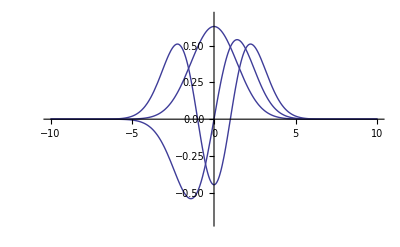

```mathematica
Show[state1,state2,state3]
```

Here we assemble them into an array (three side-by-side pairs of figures):

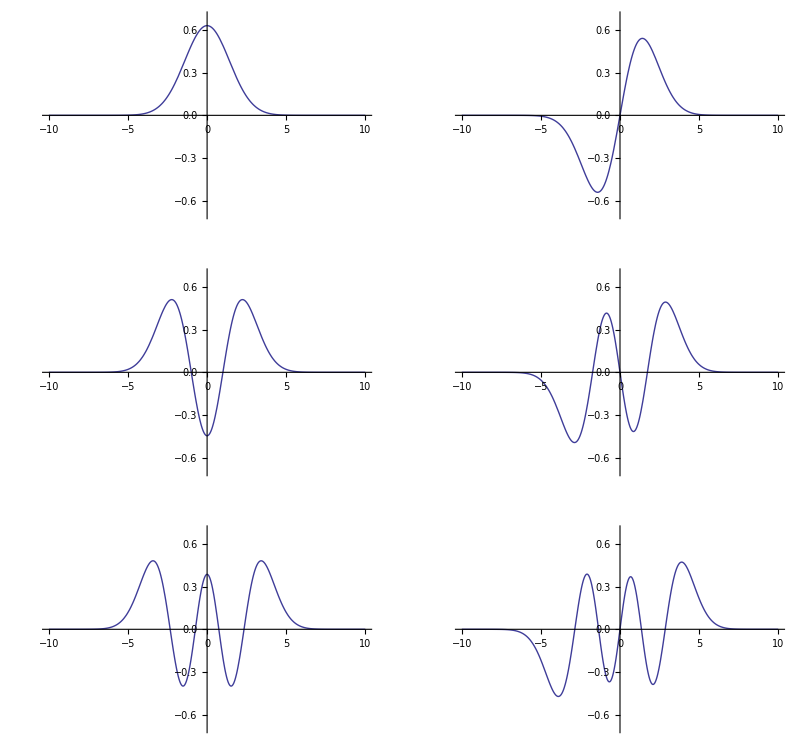

```mathematica
statesarray=Show[GraphicsGrid[{{state1, state2},{state3,state4},{state5, state6}}]]
```

Here we "box" the preceding figure:

```mathematica
GraphicsGrid[{{state1, state2},{state3,state4},{state5, state6}}, Frame->True, Ticks->None]
```

-Graphics-

The display looks crowded. We can use Spacings

```mathematica
?Spacings
```

Spacings is an option to Grid and related constructs which specifies the spacings to leave between successive objects.

to give the individual figures a bit of breathing room

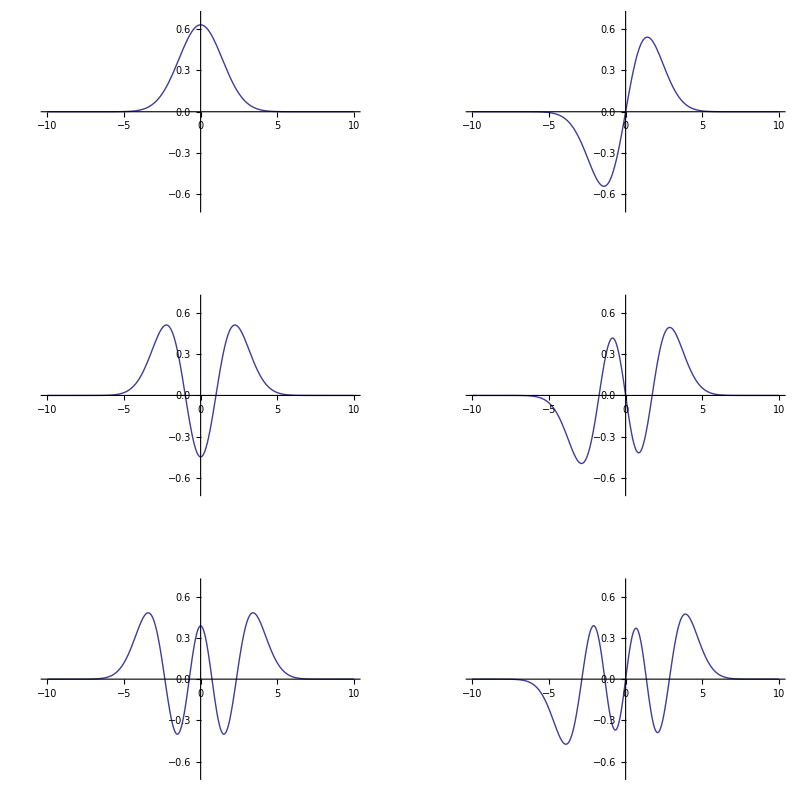

```mathematica
boxedarray=GraphicsGrid[{{state1, state2},{state3,state4},{state5, state6}}, Frame->True, Ticks->None, Spacings->{Scaled[.2],Scaled[.3]}]
```

and we can achieve a still better effect by removing the distracting ticks:

```mathematica
newstate1=Show[state1,Ticks->False];
newstate2=Show[state2,Ticks->False];
newstate3=Show[state3,Ticks->False];
newstate4=Show[state4,Ticks->False];
newstate5=Show[state5,Ticks->False];
newstate6=Show[state6,Ticks->False];
```

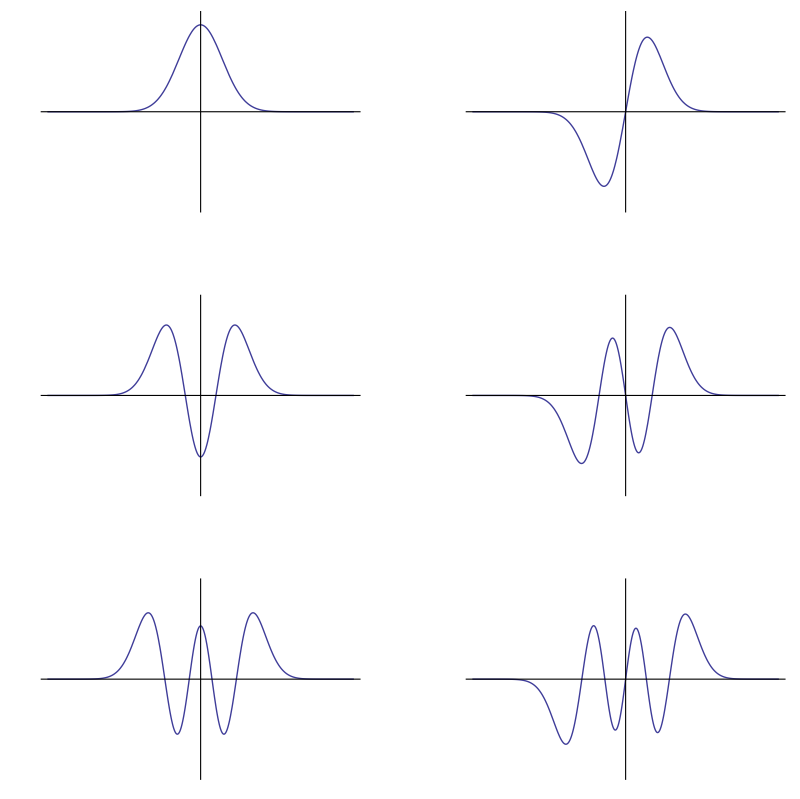

```mathematica
finalfigure=GraphicsGrid[{{newstate1, newstate2},{newstate3,newstate4},{newstate5, newstate6}}, Frame->True, Ticks->None, Spacings->{Scaled[.2],Scaled[.3]}]
```

Here is a different arrangement of the same information:

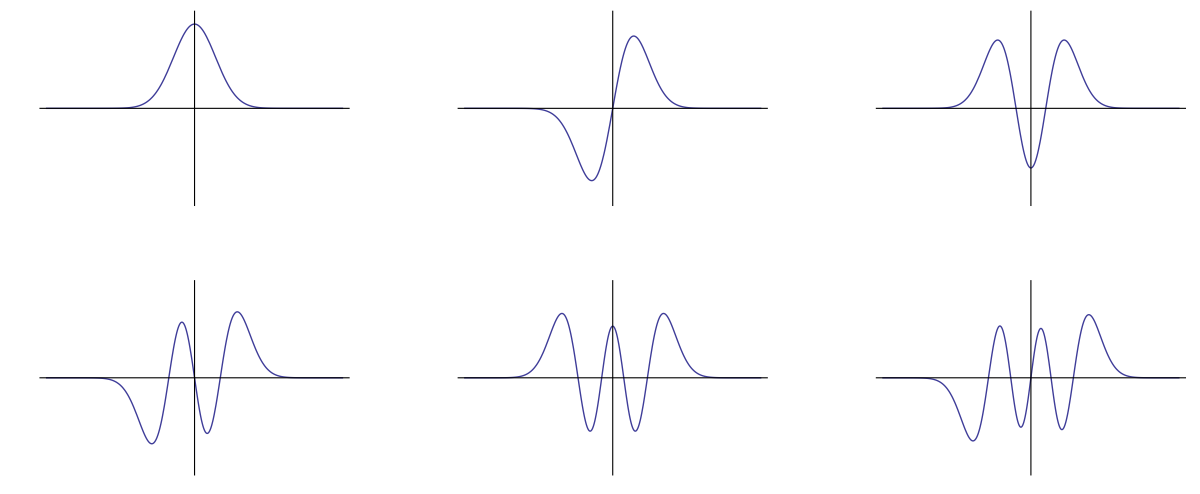

```mathematica
GraphicsGrid[{{newstate1, newstate2,newstate3},{newstate4,newstate5, newstate6}}, Frame->True, Ticks->None, Spacings->{Scaled[.2],Scaled[.3]}]
```

## Dynamic Display

This is an area in which Mathematica 6 differs most markedly from earlier versions, as becomes evident from the presence of a Dynamic Interactivity box on the Documentation Center page,  and when you click on  the Dynamic Visualization link.

### Manipulate

An alternative way to make such comparisons (on-screen, not in print!) is provided by the powerful Manipulate command, which is a new feature of Mathematica 6. For details, enter the following command

```mathematica
?Manipulate
```

Manipulate[expr,{u,u_min,u_max}] generates a version of expr with controls added to allow interactive manipulation of the value of u. 
Manipulate[expr,{u,u_min,u_max,du}] allows the value of u to vary between u_min and u_max in steps du. 
Manipulate[expr,{{u,u_init},u_min,u_max,…}] takes the initial value of u to be u_init. 
Manipulate[expr,{{u,u_init,u_lbl},…}] labels the controls for u with u_lbl. 
Manipulate[expr,{u,{u_1,u_2,…}}] allows u to take on discrete values u_1,u_2,…. 
Manipulate[expr,{u,…},{v,…},…] provides controls to manipulate each of the u,v,…. 
Manipulate[expr,c_u->{u,…},c_v->{v,…},…] links the controls to the specified controllers on an external device.

follow the » to where it leads, and (see Tutorials at the bottom of the page) click on Introduction to Manipulate.

```mathematica
Manipulate[Plot[Ψ[n,x],{x,-10,10}, PlotRange->{-0.7,0.7}],{n,0,6,1}]
```

Move the slide control (which has been set up to control the value of the integer n) to snap through the set of figures that show oscillator states of ascending order.

In the preceding figure the control parameter n ranged in discrete unit steps, from 0 to 6. In the following figure a pair of adjustable parameters range continuously:

```mathematica
Manipulate[Plot[Sin[a x+b],{x,0,2π}, Ticks->{{0,π,2π},{-1,1}}],{a,1,4},{b,0,2π}]
```

#### Example: Potential of an Electric Dipole with Adjustable Charges

I reproduce one of the Neat Examples that can be found in the Manipulate notebook, cited above:

```mathematica
Manipulate[ContourPlot[q1/Norm[{x,y}-p[[1]]]+q2/Norm[{x,y}-p[[2]]],{x,-2,2},{y,-2,2},Contours->10],{{q1,-1},-3,3},{{q2,1},-3,3},{{p,{{-1,0},{1,0}}},{-1,-1},{1,1},Locator},Deployed->True]
```

Manipulate is based upon a more fundamental resource—also new in Mathematica 6—that is described in tutorial/IntroductionToDynamic, and that pemits one to, in effect, "put knobs one equations."

#### Example

Enter the command, then slide the knob:

```mathematica
{Slider[Dynamic[n],{1,10,1}],Dynamic[Expand[(a+b)^n]]}
```

{,}

#### Example

```mathematica
{DynamicModule[{x=.5},{Slider[Dynamic[x]],Dynamic[Plot[Sin[10y x],{y,0,2Pi}]]}],
DynamicModule[{x=.5},{Slider[Dynamic[x]],Dynamic[Plot[Tan[10y x],{y,0,2Pi}]]}]}
```

{,}

#### Example: Effects Achieved by the RGBColor[ ] Command

```mathematica
Manipulate[Show[Graphics[{RGBColor[R,G,B],Disk[{0,0},1]},AspectRatio->Automatic]],{R,0,1},{G,0,1},{B,0,1}]
```

INSTRUCTIONS: Hit all three of the + buttons, then twiddle experimentally with the three slide controls. The "color coordinates" that, when inserted into RGBColor[R,G,B]  would command production of the color on display, can be read from the display windows under the respective slide controls. Given below is a variant of the same idea:

```mathematica
Manipulate[Show[Graphics[{{Opacity[0.5],RGBColor[r,g,b],Disk[{0,0},3/2]},{Opacity[0.5],RGBColor[x,y,z],Disk[{1,0},3/2]}},AspectRatio->Automatic]],{r,0,1},{g,0,1},{b,0,1},{x,0,1},{y,0,1},{z,0,1}]
```

### Animation

Another way to display how a figure moves/morphs when a variable or control parameter is made to range through its (usually continuous) set of allowed values is provided by the animation technique. To achieve animation, one asks Mathematica to use its own good sense to construct a parameterized list of figures, and then to flick through the list. The means of accomplishing such a goal differ in Mathematica 6 from those employed in earlier versions of the software, the net effect of those modifications being that animations are now very easy to construct. To read about them, command

```mathematica
?Animate
```

Animate[expr,{u,u_min,u_max}] generates an animation of expr in which u varies continuously from u_min to u_max. 
Animate[expr,{u,u_min,u_max,du}] takes u to vary in steps du. 
Animate[expr,{u,{u_1,u_2,…}}] makes u take on discrete values u_1, u_2, …. 
Animate[expr,{u,…},{v,…},…] varies all the variables u, v, ….

and follow the ».

#### Example: Motion of a Quantum Oscillator

By way of physical motivation: Suppose a quantum oscillator is initially in the equi-weighted superposition of the energy eigenstates  Ψ[m, x] and  Ψ[n, x]:

ψ[x,0]=(Ψ[m,x]+Ψ[n,x])/(√2)

At time t it will be then in the state

```mathematica
ψ[x_,t_]=(Ψ[m,x] ⅇ^(-ⅈ(m+1/2)t)+Ψ[n,x] ⅇ^(-ⅈ(n+1/2)t))/(√2)
```

((ⅇ^(-ⅈ (1/2+m) t-x^2/4) HermiteH[m,x/(√2)])/(√(2^m) (2 π)^(1/4) √(m!))+(ⅇ^(-ⅈ (1/2+n) t-x^2/4) HermiteH[n,x/(√2)])/(√(2^n) (2 π)^(1/4) √(n!)))/(√2)

The probability of finding the particle in the neighborhood of the point x at time t is given then by

P[x,t]=Conjugate[ψ[x,t]]ψ[x,t]=1/2 Ψ[m,x]^2+Ψ[m,x] Ψ[n,x] Cos[(m-n) t]+1/2 Ψ[n,x]^2

Notice that t survives only in the cross-term: quantum motion (therefore all motion) is an interference effect! We look to the case m=2 and n=3:

The red part of the following command plots P[x,t] at time t, and the remainder of the command increments t, thus generating the animation:

```mathematica
Animate[Plot[1/2 Ψ[2,x]^2+Ψ[2,x] Ψ[3,x] Cos[t]+1/2 Ψ[3,x]^2,{x,-10,10},
PlotRange->{0,0.5},
Ticks->None],{t,0,2π}, AnimationRunning->False]
```

Stop the animation, do repeated clicks on the up-control to accelerate the film, repeated clicks on the down-control to slow it down.

REMARK: The presence of the AnimationRunning->False command causes the animation to run only when when we hit the "Play" button. In the absence of that option, the figure would run all the time, which can become annoying.

#### Example: Motion of a Classical Oscillator

Here I use graphics primatives to construct the image of a particle oscillating with unit period at the end of a rubber band.

```mathematica
Animate[Show[Graphics[{
{RGBColor[0,0,1],Disk[{2+Cos[2π t],0},.1]},(*mass point*)
{GrayLevel[0.7],Rectangle[{-.1,-.5},{0,.5}]},(*left wall*)
{GrayLevel[0.7],Rectangle[{4,-.5},{4.1,.5}]},(*right wall*)
{RGBColor[1,0,0],Rectangle[{0,-.02+.01Cos[2π t]},{1.9+Cos[2π t],.02-.01Cos[2π t]}]}(*rubber band*)
}],AspectRatio->Automatic],{t,0,1}, AnimationRunning->False]
```

Note that (and how) the rubber band has been designed to get thicker as it gets shorter. The right wall was included as a way of forcing all frames to be drawn to the same scale; otherwise Mathematica would draw each to its own scale—the scale that Mathematica, in its wisdom, considers in each instance to be "optimal."

More important: notice again the method used to insert comments into the command. In long/complicated commands such comments are often helpful.

#### Example: 3D Animation

```mathematica
Animate[Plot3D[Sin[x*y+Sin[2π t]], {x,0,3},{y,0,3},Axes->None, PlotPoints->20],{t,0,1}, AnimationRunning->False]
```

To view the action from a different angle, stop the action, adjust the action, reactivate.

## Audio

Mathematica treats graphics and sound as siblings, though the former leads a very busy life while the latter is often neglected. They are controled by quite similar commands. For detailed information about Mathematica 6's audio capabilities, command

```mathematica
?Sound
```

Sound[primitives] represents a sound. 
Sound[primitives,t] specifies that the sound should have duration t.
Sound[primitives,{t_min,t_max}] specifies that the sound should extend from time t_min to time t_max.

and follow the ».

#### Example: Concert A

The function Sin[2 π 440 t]—with t interpreted to mean "time," in  seconds—describes oscillations of unit amplitude at 440 Hz. Here we listen to that function:

```mathematica
Play[Sin[2π 440 t], {t,0,3}]
```

-Graphics-

Hit the Play button to hear a 3-second sample of the tone you have produced.

#### Beats

```mathematica
Play[Sin[2π 440 t]+Sin[2π 441.5 t], {t,0,3}]
```

-Graphics-

#### Twang

```mathematica
Play[Sin[2π 440 t] ⅇ^(-t/0.2), {t,0,3}]
```

-Graphics-

#### A Non-acoustic Application of Audio

We "listen" to the function that describes (among other things) quantum state of a uniformly accelerated particle:

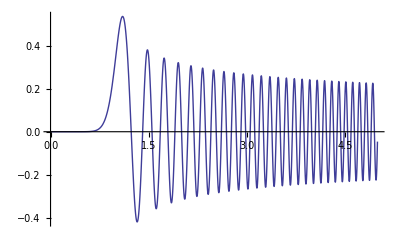

```mathematica
Plot[AiryAi[-10(x-1)],{x,0,5}]
```

```mathematica
Play[AiryAi[-100(x-.1)],{x,0,5}]
```

-Graphics-

The following examples are borrowed from the collection that are provided by the command

```mathematica
?Play
```

Play[f,{t,t_min,t_max}] creates an object that plays as a sound whose amplitude is given by f as a function of time t in seconds between t_min and t_max.

#### Another Such Example: Sound of trhe Riemann Zeta Function

```mathematica
Play[RiemannSiegelZ[1000t],{t,0,4}]
```

-Graphics-

#### Example: Five Simultaneous Pure Tones with Incommensurate Frequencies

```mathematica
Play[Sum[Sin[1000 Sqrt[n] t],{n,5}],{t,0,4}]
```

-Graphics-

#### Example: Five Simultaneous Pure Tones with Changing Frequencies

```mathematica
Play[Sum[Sin[2000 2^t n t],{n,5}],{t,0,4}]
```

-Graphics-

Mathematica possesses also some specifically musical audio capabilities. These can be read about by searching for Music/tutorial/Music, and are accessed by importing a Standard Package:

```mathematica
Needs["Music`"]
```

```mathematica
Just=MusicScale[JustMajor,256,5]
Tempered=MusicScale[TemperedMajor,256,5]
MusicScale[PythagoreanMajor,256,5]
```

-Graphics-

-Graphics-

-Graphics-

I must admit: the graphic (as oppposed to acoustic) output from audio commands was much more interesting and informative in Mathematica 5 than they have become in Mathematica 6.